```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tep/Dropbox/Mon Mac (MBP-de-admin)/Documents/GitHub/Linear-Galactic-Disk-Theory/code/nb

## Growth rate

#### Import data

#### Diffusion coefficients

```mathematica
tabqx=Import["../data/Dump_Growth_Rate_eps0_1.hf5",{"Datasets","tabqx"}];
tabGR=Import["../data/Dump_Growth_Rate_eps0_1.hf5",{"Datasets","tabGR"}]; 

GRTable=Partition[{tabqx,tabGR}//Transpose//Flatten,3];
```

#### Plot data

```mathematica
(*Generic options for the plots.*)
fontname = "Didot";
fontsize = 12;
basestyleplot = {FontFamily -> fontname,FontSize->fontsize};
labelstyleplot = {FontFamily -> fontname, FontSize -> fontsize};
imagesize = Large;(*350;*)
(*Making the plot.*)
(*Range of the plot.*)
qmin = 0.1;
qmax = 10.0;
xmin = 0.1;
xmax = 1.0;
zmin =0;
zmax = 17;
(*Axes of the plot.*)
ax = Row[{Style["q = 1 + ",fontname,fontsize],Style[FractionBox["MDH","Mdisk"]//DisplayForm,fontname,fontsize]}];
ay =  Row[{Style["x = ",fontname,fontsize],Style[FractionBox["Mdisk","Mdisk+Mbulb"]//DisplayForm,fontname,fontsize]}];
(*.*)
axstyle = {Black,Thickness[0.003]};
tickstyle = {Black,Thickness[0.003]};
(*.*)
qticks =  {{0,"0"},{1,"1"},{2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"}};
xticks =  {{0.1,"0.1"},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
zticks={1,2,3,4,5,6,7,8,9,10};
```

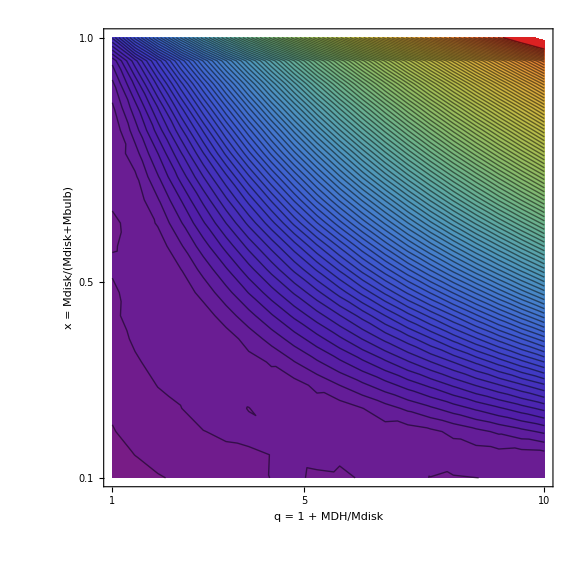

-Graphics-

```mathematica
pGR=ListContourPlot[GRTable,Contours->100,PlotRange->{All,All,{zmin,zmax}},ColorFunction->"Rainbow",FrameLabel->{ax,ay},BaseStyle->basestyleplot,LabelStyle->labelstyleplot,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][#]&),{zmin,zmax}},LegendLabel->"Growth rate",Method->{FrameStyle->axstyle,TicksStyle->tickstyle,Ticks->{{0,"0"},(*{0.25,""},{0.5,"0.5"},{0.75,""},*){1,""},(*{1.25,""},{1.5,"1.5"},{1.75,""},*){2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"},{11,""},{12,""},{13,""},{14,""},{15,"15"},{16,""},{17,""}}}],Above],ImageSize->imagesize,FrameTicks->{qticks,xticks},FrameStyle->{axstyle,axstyle,axstyle,axstyle},PlotRangePadding->None]
pGR=Rasterize[pGR,RasterSize->1000];
pDensGR=ListPlot3D[GRTable,PlotRange->{{qmin,qmax},{xmin,xmax},All},ColorFunction->"Rainbow",BaseStyle->basestyleplot,LabelStyle->labelstyleplot,ImageSize->imagesize,PlotRangePadding->None,AxesLabel->{ax,ay,"GR"}];
pDensGR=Rasterize[pDensGR,RasterSize->1000]
```

#### Save data

```mathematica
Export["../graphs/growthRate_eps0_1.png",pGR]
Export["../graphs/growthRate3D_eps0_1.png",pDensGR]
```

../graphs/growthRate_eps0_1.png

../graphs/growthRate3D_eps0_1.png

## Growth rate (mass fraction)

#### Import data

#### Diffusion coefficients

```mathematica
tabfrac=Import["../data/Dump_Growth_Rate_frac_eps0_1.hf5",{"Datasets","tabfrac"}];
tabGR=Import["../data/Dump_Growth_Rate_frac_eps0_1.hf5",{"Datasets","tabGR"}]; 

GRTable=Partition[{tabfrac,tabGR}//Transpose//Flatten,3];
```

#### Plot data

```mathematica
(*Generic options for the plots.*)
fontname = "Didot";
fontsize = 12;
basestyleplot = {FontFamily -> fontname,FontSize->fontsize};
labelstyleplot = {FontFamily -> fontname, FontSize -> fontsize};
imagesize = Large(*350*);
(*Making the plot.*)
(*Range of the plot.*)
fDHmin = 0.0;
fDHmax = 10.0;
xmin = 0.1;
xmax = 1.0;
zmin =0;
zmax = 18;
(*Axes of the plot.*)
ax = Row[{Style[FractionBox["MDH","M"]//DisplayForm,fontname,fontsize]}];
ay =  Row[{Style[FractionBox["Mdisk","M"]//DisplayForm,fontname,fontsize]}];
(*.*)
axstyle = {Black,Thickness[0.003]};
tickstyle = {Black,Thickness[0.003]};
(*.*)
fDHticks = {{0,"0"},{1,""},{2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"}};
xticks =  {{0.0,"0.0"},{0.1,"0.1"},{0.2,""},{0.3,""},{0.4,""},{0.5,"0.5"},{0.6,""},{0.7,""},{0.8,""},{0.9,""},{1.0,"1.0"}};
zticks={1,2,3,4,5,6,7,8,9,10};
```

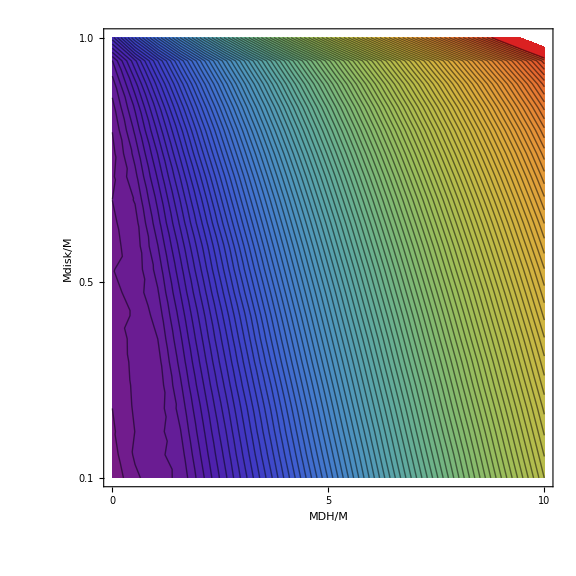

-Graphics-

```mathematica
pGR=ListContourPlot[GRTable,Contours->100,PlotRange->{All,All,{zmin,zmax}},ColorFunction->"Rainbow",FrameLabel->{ax,ay},BaseStyle->basestyleplot,LabelStyle->labelstyleplot,PlotLegends->Placed[BarLegend[{(ColorData["Rainbow"][#]&),{zmin,zmax}},LegendLabel->"Growth rate",Method->{FrameStyle->axstyle,TicksStyle->tickstyle,Ticks->{{0,"0"},{1,""},{2,""},{3,""},{4,""},{5,"5"},{6,""},{7,""},{8,""},{9,""},{10,"10"},{11,""},{12,""},{13,""},{14,""},{15,"15"},{16,""},{17,""},{18,""}}}],Above],ImageSize->imagesize,FrameTicks->{aticks,xticks},FrameStyle->{axstyle,axstyle,axstyle,axstyle},PlotRangePadding->None]
pGR=Rasterize[pGR,RasterSize->1000];
pDensGR=ListPlot3D[GRTable,PlotRange->{{fDHmin,fDHmax},{xmin,xmax},All},ColorFunction->"Rainbow",BaseStyle->basestyleplot,LabelStyle->labelstyleplot,ImageSize->imagesize,PlotRangePadding->None,AxesLabel->{ax,ay,"GR"}];
pDensGR=Rasterize[pDensGR,RasterSize->1000]
```

```mathematica
Export["../graphs/growthRatefrac_eps0_1.png",pGR]
Export["../graphs/growthRate3Dfrac_eps0_1.png",pDensGR]
```

../graphs/growthRatefrac_eps0_1.png

../graphs/growthRate3Dfrac_eps0_1.png